```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 379 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
(* There is this issue again with components , versus v^2 written as components dotted with each other *) 
(* Also , { r, ϕ , θ } convention NOT { r, θ , ϕ } *)
```

```mathematica
Clear[s1]
s1 = { r[t] Cos[ϕ[t]] Sin[θ[t]] , r[t] Sin[ϕ[t]] Sin[θ[t]] , r[t] Cos[θ[t]] }
```

{Cos[ϕ[t]] r[t] Sin[θ[t]],r[t] Sin[θ[t]] Sin[ϕ[t]],Cos[θ[t]] r[t]}

```mathematica
D[s1, t]
```

{Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t],Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t],Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t]}

```mathematica
D[s1, t] . D[s1, t]
```

(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2+(Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t])^2+(Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t])^2

```mathematica
D[s1, t] . D[s1, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Cos[ϕ[t]]^2 Sin[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 Sin[ϕ[t]]^2 r'[t]^2-2 Cos[θ[t]] r[t] Sin[θ[t]] r'[t] θ'[t]+2 Cos[θ[t]] Cos[ϕ[t]]^2 r[t] Sin[θ[t]] r'[t] θ'[t]+2 Cos[θ[t]] r[t] Sin[θ[t]] Sin[ϕ[t]]^2 r'[t] θ'[t]+Cos[θ[t]]^2 Cos[ϕ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2+Cos[θ[t]]^2 r[t]^2 Sin[ϕ[t]]^2 θ'[t]^2+Cos[ϕ[t]]^2 r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2+r[t]^2 Sin[θ[t]]^2 Sin[ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[s1, t] . D[s1, t]  // Expand  // Simplify // Expand
```

r'[t]^2+r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2

```mathematica
Sqrt[Expand[Simplify[Expand[ D[s1, t] . D[s1, t] ] ] ][[1]]] // PowerExpand
Sqrt[Expand[Simplify[Expand[ D[s1, t] . D[s1, t] ] ] ][[2]]] // PowerExpand
Sqrt[Expand[Simplify[Expand[ D[s1, t] . D[s1, t] ] ] ][[3]]] // PowerExpand
```

r'[t]

r[t] θ'[t]

r[t] Sin[θ[t]] ϕ'[t]

```mathematica
Clear[v1]
v1 = 
Table[ 
Sqrt[Expand[Simplify[Expand[ D[s1, t] . D[s1, t] ] ] ][[i]]] // PowerExpand , { i, 1, 3 } ]
```

{r'[t],r[t] θ'[t],r[t] Sin[θ[t]] ϕ'[t]}

```mathematica
v1 . v1
```

r'[t]^2+r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2

```mathematica
v1 .v1 == D[s1, t] . D[s1, t] // Expand // Simplify
```

True

```mathematica
Clear[v2]
v2 = 
{r'[t] , 0 , ( l - r[t] ) β'[t] Sin[π-α] }
```

{r'[t],0,(l-r[t]) Sin[α] β'[t]}

```mathematica
v2 . v2
```

r'[t]^2+(l-r[t])^2 Sin[α]^2 β'[t]^2

```mathematica
Clear[T] 
T = 1/2 m ( v1 . v1  ) + 1/2 m ( v2 . v2  ) // Expand // Simplify  ;
T // pdConv
```

1/2 m (sin^2(α) (l-r(t))^2 ((∂β(t))/(∂t))^2+(r(t))^2 (sin^2(θ(t)) ((∂ϕ(t))/(∂t))^2+((∂θ(t))/(∂t))^2)+2 ((∂r(t))/(∂t))^2)

```mathematica
V = m g r[t] Cos[θ[t]] - m g ( l - r[t] ) Cos[α]
```

-g m Cos[α] (l-r[t])+g m Cos[θ[t]] r[t]

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // pdConv
```

g m cos(α) (l-r(t))-g m r(t) cos(θ(t))+1/2 m (sin^2(α) (l-r(t))^2 ((∂β(t))/(∂t))^2+(r(t))^2 (sin^2(θ(t)) ((∂ϕ(t))/(∂t))^2+((∂θ(t))/(∂t))^2)+2 ((∂r(t))/(∂t))^2)

```mathematica
Clear[q]
q = { r[t] , θ[t] , ϕ[t] , β[t] } 
Clear[𝓆]
𝓆 = { r , θ , ϕ , β }
```

{r[t],θ[t],ϕ[t],β[t]}

{r,θ,ϕ,β}

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

m (-g Cos[α]-g Cos[θ[t]]-(l-r[t]) Sin[α]^2 β'[t]^2+r[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)-2 r''[t])==0
m r[t] (g Sin[θ[t]]-2 r'[t] θ'[t]+r[t] (Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2-θ''[t]))==0
-m r[t] Sin[θ[t]] (2 Sin[θ[t]] r'[t] ϕ'[t]+r[t] (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t]))==0
m (l-r[t]) Sin[α]^2 (2 r'[t] β'[t]+(-l+r[t]) β''[t])==0

```mathematica
Clear[parameters]
parameters = {
m-> 1 , 
g-> 9.8 , 
α -> π/12 ,
l-> 2
} ;
parameters // TableForm
```

m→1
g→9.8
α→π/12
l→2

```mathematica
eqs /. parameters  // Expand  // TableForm
```

-9.46607-9.8 Cos[θ[t]]-β'[t]^2+1/2 √3 β'[t]^2+1/2 r[t] β'[t]^2-1/4 √3 r[t] β'[t]^2+r[t] θ'[t]^2+r[t] Sin[θ[t]]^2 ϕ'[t]^2-2 r''[t]==0
9.8 r[t] Sin[θ[t]]-2 r[t] r'[t] θ'[t]+Cos[θ[t]] r[t]^2 Sin[θ[t]] ϕ'[t]^2-r[t]^2 θ''[t]==0
-2 r[t] Sin[θ[t]]^2 r'[t] ϕ'[t]-2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t] ϕ'[t]-r[t]^2 Sin[θ[t]]^2 ϕ''[t]==0
2 r'[t] β'[t]-√3 r'[t] β'[t]-r[t] r'[t] β'[t]+1/2 √3 r[t] r'[t] β'[t]-2 β''[t]+√3 β''[t]+2 r[t] β''[t]-√3 r[t] β''[t]-1/2 r[t]^2 β''[t]+1/4 √3 r[t]^2 β''[t]==0

```mathematica
Clear[ics]
ics = { 
r[0] == 0.1 ,
r'[0] == 0.1 ,
θ[0] == 0.1 , 
θ'[0] == 0.1 ,
ϕ[0] == 0.1 ,
ϕ'[0] == 0.1 ,
β[0] == 0.1 ,
β'[0] ==  0.1 
};
ics // TableForm
```

r[0]==0.1
r'[0]==0.1
θ[0]==0.1
θ'[0]==0.1
ϕ[0]==0.1
ϕ'[0]==0.1
β[0]==0.1
β'[0]==0.1

```mathematica
Clear[solution]
solution[t_] =
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0 , 100 } ]]
```

{r[t]→InterpolatingFunction[{{0., 100.}}, <>][t],θ[t]→InterpolatingFunction[{{0., 100.}}, <>][t],ϕ[t]→InterpolatingFunction[{{0., 100.}}, <>][t],β[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ], { t, 0, 10 } , PlotLabels-> q  ]
```

-Graphics-

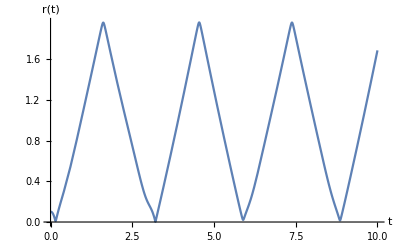

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t , q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```

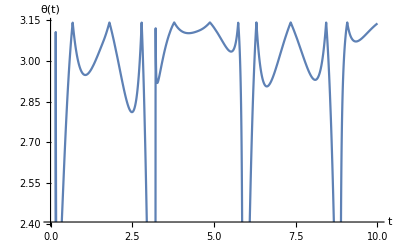

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t , q[[2]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] }  ]  ,
{ tmax , 1 ,10 , 0.5  } ]
```

```mathematica
D[ ℒ , D[q[[3]], t] ] 
D[ ℒ , D[q[[4]], t] ] 
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ]  // Expand // Simplify 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]  // Expand // Simplify
```

m r[t]^2 Sin[θ[t]]^2 ϕ'[t]

m (l-r[t])^2 Sin[α]^2 β'[t]

m (g Cos[α]+g Cos[θ[t]]+(l-r[t]) Sin[α]^2 β'[t]^2-r[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r''[t])

m r[t] (-g Sin[θ[t]]+2 r'[t] θ'[t]+r[t] (-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]))

```mathematica
Clear[com]
com = FirstIntegrals[ ℒ , q, t ]  ;
com // TableForm
```

FirstIntegral[ϕ]→-m r[t]^2 Sin[θ[t]]^2 ϕ'[t]
FirstIntegral[β]→-m (l-r[t])^2 Sin[α]^2 β'[t]
FirstIntegral[t]→1/2 m (2 r'[t]^2+2 r[t] (g (Cos[α]+Cos[θ[t]])-l Sin[α]^2 β'[t]^2)+l (-2 g Cos[α]+l Sin[α]^2 β'[t]^2)+r[t]^2 (Sin[α]^2 β'[t]^2+θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))

```mathematica
Clear[𝓅]
𝓅 = 
Map[ p , q ]
```

{p[r[t]],p[θ[t]],p[ϕ[t]],p[β[t]]}

```mathematica
D[ ℒ , D[q[[1]], t] ] == 𝓅[[1]] 
D[ ℒ , D[q[[2]], t] ] == 𝓅[[2]] 
D[ ℒ , D[q[[3]], t] ] == 𝓅[[3]] 
D[ ℒ , D[q[[4]], t] ] == 𝓅[[4]]
```

2 m r'[t]==p[r[t]]

m r[t]^2 θ'[t]==p[θ[t]]

m r[t]^2 Sin[θ[t]]^2 ϕ'[t]==p[ϕ[t]]

m (l-r[t])^2 Sin[α]^2 β'[t]==p[β[t]]

```mathematica
Clear[momenta]
momenta = 
Flatten[Solve[Table[D[ ℒ , D[q[[i]], t] ]  == 𝓅[[i]] , { i, 1, Length[𝓅] } ]  , D[q, t] ]] ;
momenta // TableForm
```

r'[t]→p[r[t]]/(2 m)
θ'[t]→p[θ[t]]/(m r[t]^2)
ϕ'[t]→(Csc[θ[t]]^2 p[ϕ[t]])/(m r[t]^2)
β'[t]→(Csc[α]^2 p[β[t]])/(m (l-r[t])^2)

```mathematica
Clear[ℋ]
ℋ = 
( Sum[ 𝓅[[i]] D[q[[i]], t] , { i, 1, Length[𝓅] } ] - ℒ )   /. momenta // Expand
```

-g l m Cos[α]+p[r[t]]^2/(4 m)+(Csc[α]^2 p[β[t]]^2)/(2 m (l-r[t])^2)+p[θ[t]]^2/(2 m r[t]^2)+(Csc[θ[t]]^2 p[ϕ[t]]^2)/(2 m r[t]^2)+g m Cos[α] r[t]+g m Cos[θ[t]] r[t]

```mathematica
Clear[pReplace]
pReplace[q_,𝓆_]:= 
Table[
Map[p,q][[i]] -> p[ 𝓆[[i]] ][t]  , 
{ i , 1 , Length[q] } ] 
(* Or get rid of the [t] so that it's just p[θ] and p[z] or p subscript theta  *)
```

```mathematica
Clear[pReplace2]
pReplace2[q_,𝓆_]:= 
Table[
Map[p,q][[i]] -> Subscript[ p , 𝓆[[i]] ]   , 
{ i , 1 , Length[q] } ]
```

```mathematica
Clear[pReplace3]
pReplace3[q_,𝓆_]:= 
Table[
Map[p,q][[i]] -> Subscript[ p , 𝓆[[i]] ][t]   , 
{ i , 1 , Length[q] } ]
```

```mathematica
pReplace[q,𝓆] // TableForm
pReplace2[q,𝓆] // TableForm
pReplace3[q,𝓆] // TableForm
```

p[r[t]]→p[r][t]
p[θ[t]]→p[θ][t]
p[ϕ[t]]→p[ϕ][t]
p[β[t]]→p[β][t]

p[r[t]]→p_r
p[θ[t]]→p_θ
p[ϕ[t]]→p_ϕ
p[β[t]]→p_β

p[r[t]]→p_r[t]
p[θ[t]]→p_θ[t]
p[ϕ[t]]→p_ϕ[t]
p[β[t]]→p_β[t]

```mathematica
ℋ /. pReplace[q,𝓆]
```

-g l m Cos[α]+g m Cos[α] r[t]+g m Cos[θ[t]] r[t]+(p[r][t])^2/(4 m)+(Csc[α]^2 (p[β][t])^2)/(2 m (l-r[t])^2)+(p[θ][t])^2/(2 m r[t]^2)+(Csc[θ[t]]^2 (p[ϕ][t])^2)/(2 m r[t]^2)

```mathematica
ℋ /. pReplace2[q,𝓆] // TraditionalForm (* This is EFFING RIGHT !!!!! *)
```

-g l m cos(α)+g m cos(α) r(t)+g m r(t) cos(θ(t))+(csc^2(α) p_β^2)/(2 m (l-r(t))^2)+(p_ϕ^2 csc^2(θ(t)))/(2 m (r(t))^2)+p_θ^2/(2 m (r(t))^2)+p_r^2/(4 m)

```mathematica
ℋ /. pReplace3[q,𝓆] // TraditionalForm
```

-g l m cos(α)+g m cos(α) r(t)+g m r(t) cos(θ(t))+(csc^2(α) (p_β(t))^2)/(2 m (l-r(t))^2)+((p_ϕ(t))^2 csc^2(θ(t)))/(2 m (r(t))^2)+(p_θ(t))^2/(2 m (r(t))^2)+(p_r(t))^2/(4 m)